```mathematica
F[n_]:=Sum[Exp[-n^n(Sin[(n*Pi)/j])^2],{j,1,n}]
```

```mathematica
K[n_,j_]:=Exp[-n^n(Sin[(n*Pi)/j])^2]
```

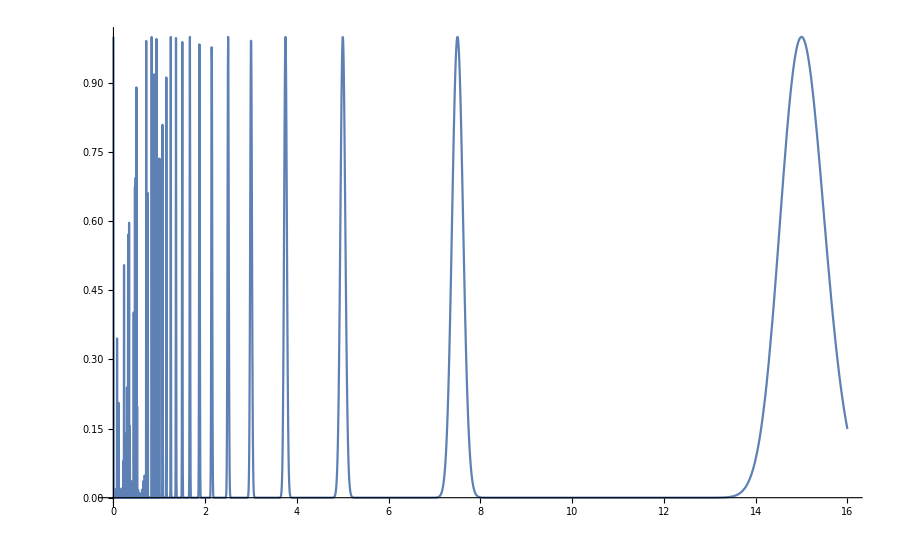

```mathematica
Plot[K[15, x],  {x,0,16}, PlotRange->{0,1}]
```

```mathematica
IntegerPart[N[F[15]]]
```

4

```mathematica
K[15,1]
```

1

```mathematica
B[n_]:=IntegerPart[N[Exp[-50000(Sin[(2*Pi)/IntegerPart[N[F[n]]]])^2]]]
```

```mathematica
B[149]
```

1

```mathematica
N[F[149]]
```

2.

```mathematica
B[5]
```

1.

```mathematica
IntegerPart[1.]
```

1

```mathematica
U[j_]:=Module[
{n,k,NP},
NP=True;
k=1;
n =2*B[j];

While[NP,
n=n+2*Product[(1-B[j+2i]),{i,1,k}] ;

If[(1-B[j+2k])==0,
NP=False;
];

(*Print["(1-B[j+2k])=",(1-B[j+2k])," and k = ",k];*)

k++;
];

Return[n];
];
```

```mathematica
p=1;
l=1;
Do[
l=U[p]+p;
p=l;
Print["The ",i,"th prime is ",p"."]
,{i,1,1000}]
```

The 1th prime is 3 .

The 2th prime is 5 .

The 3th prime is 7 .

The 4th prime is 11 .

The 5th prime is 13 .

The 6th prime is 17 .

The 7th prime is 19 .

The 8th prime is 23 .

The 9th prime is 29 .

The 10th prime is 31 .

The 11th prime is 37 .

The 12th prime is 41 .

The 13th prime is 43 .

The 14th prime is 47 .

The 15th prime is 53 .

The 16th prime is 59 .

The 17th prime is 61 .

The 18th prime is 67 .

The 19th prime is 71 .

The 20th prime is 73 .

The 21th prime is 79 .

The 22th prime is 83 .

The 23th prime is 89 .

The 24th prime is 97 .

The 25th prime is 101 .

The 26th prime is 103 .

The 27th prime is 107 .

The 28th prime is 109 .

The 29th prime is 113 .

The 30th prime is 127 .

The 31th prime is 131 .

The 32th prime is 137 .

The 33th prime is 139 .

The 34th prime is 149 .

The 35th prime is 151 .

The 36th prime is 157 .

The 37th prime is 163 .

The 38th prime is 167 .

The 39th prime is 173 .

The 40th prime is 179 .

The 41th prime is 181 .

The 42th prime is 191 .

The 43th prime is 193 .

The 44th prime is 197 .

The 45th prime is 199 .

The 46th prime is 211 .

The 47th prime is 223 .

The 48th prime is 227 .

The 49th prime is 229 .

The 50th prime is 233 .

The 51th prime is 239 .

The 52th prime is 241 .

The 53th prime is 251 .

The 54th prime is 257 .

The 55th prime is 263 .

The 56th prime is 269 .

The 57th prime is 271 .

The 58th prime is 277 .

The 59th prime is 281 .

The 60th prime is 283 .

The 61th prime is 293 .

The 62th prime is 307 .

The 63th prime is 311 .

The 64th prime is 313 .

The 65th prime is 317 .

The 66th prime is 331 .

The 67th prime is 337 .

The 68th prime is 347 .

The 69th prime is 349 .

The 70th prime is 353 .

The 71th prime is 359 .

The 72th prime is 367 .

The 73th prime is 373 .

The 74th prime is 379 .

The 75th prime is 383 .

The 76th prime is 389 .

The 77th prime is 397 .

The 78th prime is 401 .

The 79th prime is 409 .

The 80th prime is 419 .

The 81th prime is 421 .

The 82th prime is 431 .

The 83th prime is 433 .

The 84th prime is 439 .

The 85th prime is 443 .

The 86th prime is 449 .

The 87th prime is 457 .

The 88th prime is 461 .

The 89th prime is 463 .

The 90th prime is 467 .

The 91th prime is 479 .

The 92th prime is 487 .

The 93th prime is 491 .

The 94th prime is 499 .

The 95th prime is 503 .

The 96th prime is 509 .

The 97th prime is 521 .

The 98th prime is 523 .

The 99th prime is 541 .

The 100th prime is 547 .

The 101th prime is 557 .

The 102th prime is 563 .

The 103th prime is 569 .

The 104th prime is 571 .

The 105th prime is 577 .

The 106th prime is 587 .

The 107th prime is 593 .

The 108th prime is 599 .

The 109th prime is 601 .

The 110th prime is 607 .

The 111th prime is 613 .

The 112th prime is 617 .

The 113th prime is 619 .

The 114th prime is 631 .

The 115th prime is 641 .

The 116th prime is 643 .

The 117th prime is 647 .

The 118th prime is 653 .

The 119th prime is 659 .

The 120th prime is 661 .

The 121th prime is 673 .

The 122th prime is 677 .

The 123th prime is 683 .

The 124th prime is 691 .

The 125th prime is 701 .

The 126th prime is 709 .

The 127th prime is 719 .

The 128th prime is 727 .

The 129th prime is 733 .

The 130th prime is 739 .

The 131th prime is 743 .

The 132th prime is 751 .

The 133th prime is 757 .

The 134th prime is 761 .

The 135th prime is 769 .

The 136th prime is 773 .

The 137th prime is 787 .

The 138th prime is 797 .

The 139th prime is 809 .

The 140th prime is 811 .

The 141th prime is 821 .

The 142th prime is 823 .

The 143th prime is 827 .

The 144th prime is 829 .

The 145th prime is 839 .

The 146th prime is 853 .

The 147th prime is 857 .

The 148th prime is 859 .

The 149th prime is 863 .

The 150th prime is 877 .

The 151th prime is 881 .

The 152th prime is 883 .

The 153th prime is 887 .

The 154th prime is 907 .

The 155th prime is 911 .

The 156th prime is 919 .

The 157th prime is 929 .

The 158th prime is 937 .

The 159th prime is 941 .

The 160th prime is 947 .

The 161th prime is 953 .

The 162th prime is 967 .

The 163th prime is 971 .

The 164th prime is 977 .

The 165th prime is 983 .

The 166th prime is 991 .

The 167th prime is 997 .

The 168th prime is 1009 .

The 169th prime is 1013 .

The 170th prime is 1019 .

The 171th prime is 1021 .

The 172th prime is 1031 .

The 173th prime is 1033 .

The 174th prime is 1039 .

The 175th prime is 1049 .

The 176th prime is 1051 .

The 177th prime is 1061 .

The 178th prime is 1063 .

The 179th prime is 1069 .

The 180th prime is 1087 .

The 181th prime is 1091 .

The 182th prime is 1093 .

The 183th prime is 1097 .

The 184th prime is 1103 .

The 185th prime is 1109 .

The 186th prime is 1117 .

The 187th prime is 1123 .

The 188th prime is 1129 .

The 189th prime is 1151 .

The 190th prime is 1153 .

The 191th prime is 1163 .

The 192th prime is 1171 .

The 193th prime is 1181 .

The 194th prime is 1187 .

The 195th prime is 1193 .

The 196th prime is 1201 .

The 197th prime is 1213 .

The 198th prime is 1217 .

The 199th prime is 1223 .

The 200th prime is 1229 .

The 201th prime is 1231 .

The 202th prime is 1237 .

The 203th prime is 1249 .

The 204th prime is 1259 .

The 205th prime is 1277 .

The 206th prime is 1279 .

The 207th prime is 1283 .

The 208th prime is 1289 .

The 209th prime is 1291 .

The 210th prime is 1297 .

The 211th prime is 1301 .

The 212th prime is 1303 .

The 213th prime is 1307 .

The 214th prime is 1319 .

The 215th prime is 1321 .

The 216th prime is 1327 .

The 217th prime is 1361 .

The 218th prime is 1367 .

The 219th prime is 1373 .

The 220th prime is 1381 .

The 221th prime is 1399 .

The 222th prime is 1409 .

The 223th prime is 1423 .

The 224th prime is 1427 .

The 225th prime is 1429 .

The 226th prime is 1433 .

The 227th prime is 1439 .

The 228th prime is 1447 .

The 229th prime is 1451 .

The 230th prime is 1453 .

The 231th prime is 1459 .

The 232th prime is 1471 .

The 233th prime is 1481 .

The 234th prime is 1483 .

The 235th prime is 1487 .

The 236th prime is 1489 .

The 237th prime is 1493 .

The 238th prime is 1499 .

The 239th prime is 1511 .

The 240th prime is 1523 .

The 241th prime is 1531 .

The 242th prime is 1543 .

The 243th prime is 1549 .

The 244th prime is 1553 .

The 245th prime is 1559 .

The 246th prime is 1567 .

The 247th prime is 1571 .

The 248th prime is 1579 .

The 249th prime is 1583 .

The 250th prime is 1597 .

The 251th prime is 1601 .

The 252th prime is 1607 .

The 253th prime is 1609 .

The 254th prime is 1613 .

The 255th prime is 1619 .

The 256th prime is 1621 .

The 257th prime is 1627 .

The 258th prime is 1637 .

The 259th prime is 1657 .

The 260th prime is 1663 .

The 261th prime is 1667 .

The 262th prime is 1669 .

The 263th prime is 1693 .

The 264th prime is 1697 .

The 265th prime is 1699 .

The 266th prime is 1709 .

The 267th prime is 1721 .

The 268th prime is 1723 .

The 269th prime is 1733 .

The 270th prime is 1741 .

The 271th prime is 1747 .

The 272th prime is 1753 .

The 273th prime is 1759 .

The 274th prime is 1777 .

The 275th prime is 1783 .

The 276th prime is 1787 .

The 277th prime is 1789 .

The 278th prime is 1801 .

The 279th prime is 1811 .

The 280th prime is 1823 .

The 281th prime is 1831 .

The 282th prime is 1847 .

The 283th prime is 1861 .

The 284th prime is 1867 .

The 285th prime is 1871 .

The 286th prime is 1873 .

The 287th prime is 1877 .

The 288th prime is 1879 .

The 289th prime is 1889 .

The 290th prime is 1901 .

The 291th prime is 1907 .

The 292th prime is 1913 .

The 293th prime is 1931 .

The 294th prime is 1933 .

The 295th prime is 1949 .

The 296th prime is 1951 .

The 297th prime is 1973 .

The 298th prime is 1979 .

The 299th prime is 1987 .

The 300th prime is 1993 .

The 301th prime is 1997 .

The 302th prime is 1999 .

The 303th prime is 2003 .

The 304th prime is 2011 .

The 305th prime is 2017 .

The 306th prime is 2027 .

The 307th prime is 2029 .

The 308th prime is 2039 .

The 309th prime is 2053 .

The 310th prime is 2063 .

The 311th prime is 2069 .

The 312th prime is 2081 .

The 313th prime is 2083 .

The 314th prime is 2087 .

The 315th prime is 2089 .

The 316th prime is 2099 .

The 317th prime is 2111 .

The 318th prime is 2113 .

The 319th prime is 2129 .

The 320th prime is 2131 .

The 321th prime is 2137 .

The 322th prime is 2141 .

The 323th prime is 2143 .

The 324th prime is 2153 .

The 325th prime is 2161 .

The 326th prime is 2179 .

The 327th prime is 2203 .

The 328th prime is 2207 .

The 329th prime is 2213 .

The 330th prime is 2221 .

The 331th prime is 2237 .

The 332th prime is 2239 .

The 333th prime is 2243 .

The 334th prime is 2251 .

The 335th prime is 2267 .

The 336th prime is 2269 .

The 337th prime is 2273 .

The 338th prime is 2281 .

The 339th prime is 2287 .

The 340th prime is 2293 .

The 341th prime is 2297 .

The 342th prime is 2309 .

The 343th prime is 2311 .

The 344th prime is 2333 .

The 345th prime is 2339 .

The 346th prime is 2341 .

The 347th prime is 2347 .

The 348th prime is 2351 .

The 349th prime is 2357 .

The 350th prime is 2371 .

The 351th prime is 2377 .

The 352th prime is 2381 .

The 353th prime is 2383 .

The 354th prime is 2389 .

The 355th prime is 2393 .

The 356th prime is 2399 .

The 357th prime is 2411 .

The 358th prime is 2417 .

The 359th prime is 2423 .

The 360th prime is 2437 .

The 361th prime is 2441 .

The 362th prime is 2447 .

The 363th prime is 2459 .

The 364th prime is 2467 .

The 365th prime is 2473 .

The 366th prime is 2477 .

The 367th prime is 2503 .

The 368th prime is 2521 .

The 369th prime is 2531 .

The 370th prime is 2539 .

The 371th prime is 2543 .

The 372th prime is 2549 .

The 373th prime is 2551 .

The 374th prime is 2557 .

The 375th prime is 2579 .

The 376th prime is 2591 .

The 377th prime is 2593 .

The 378th prime is 2609 .

The 379th prime is 2617 .

The 380th prime is 2621 .

The 381th prime is 2633 .

The 382th prime is 2647 .

The 383th prime is 2657 .

The 384th prime is 2659 .

The 385th prime is 2663 .

The 386th prime is 2671 .

The 387th prime is 2677 .

The 388th prime is 2683 .

The 389th prime is 2687 .

The 390th prime is 2689 .

The 391th prime is 2693 .

The 392th prime is 2699 .

The 393th prime is 2707 .

The 394th prime is 2711 .

The 395th prime is 2713 .

The 396th prime is 2719 .

The 397th prime is 2729 .

The 398th prime is 2731 .

The 399th prime is 2741 .

The 400th prime is 2749 .

The 401th prime is 2753 .

The 402th prime is 2767 .

The 403th prime is 2777 .

The 404th prime is 2789 .

The 405th prime is 2791 .

The 406th prime is 2797 .

The 407th prime is 2801 .

The 408th prime is 2803 .

The 409th prime is 2819 .

The 410th prime is 2833 .

The 411th prime is 2837 .

The 412th prime is 2843 .

The 413th prime is 2851 .

The 414th prime is 2857 .

The 415th prime is 2861 .

The 416th prime is 2879 .

The 417th prime is 2887 .

The 418th prime is 2897 .

The 419th prime is 2903 .

The 420th prime is 2909 .

The 421th prime is 2917 .

The 422th prime is 2927 .

The 423th prime is 2939 .

The 424th prime is 2953 .

The 425th prime is 2957 .

The 426th prime is 2963 .

The 427th prime is 2969 .

The 428th prime is 2971 .

The 429th prime is 2999 .

The 430th prime is 3001 .

The 431th prime is 3011 .

The 432th prime is 3019 .

The 433th prime is 3023 .

The 434th prime is 3037 .

The 435th prime is 3041 .

The 436th prime is 3049 .

The 437th prime is 3061 .

The 438th prime is 3067 .

The 439th prime is 3079 .

The 440th prime is 3083 .

The 441th prime is 3089 .

The 442th prime is 3109 .

The 443th prime is 3119 .

The 444th prime is 3121 .

The 445th prime is 3137 .

The 446th prime is 3163 .

The 447th prime is 3167 .

The 448th prime is 3169 .

The 449th prime is 3181 .

The 450th prime is 3187 .

The 451th prime is 3191 .

The 452th prime is 3203 .

The 453th prime is 3209 .

The 454th prime is 3217 .

The 455th prime is 3221 .

The 456th prime is 3229 .

The 457th prime is 3251 .

The 458th prime is 3253 .

The 459th prime is 3257 .

The 460th prime is 3259 .

The 461th prime is 3271 .

The 462th prime is 3299 .

The 463th prime is 3301 .

The 464th prime is 3307 .

The 465th prime is 3313 .

The 466th prime is 3319 .

The 467th prime is 3323 .

The 468th prime is 3329 .

The 469th prime is 3331 .

The 470th prime is 3343 .

The 471th prime is 3347 .

The 472th prime is 3359 .

The 473th prime is 3361 .

The 474th prime is 3371 .

The 475th prime is 3373 .

The 476th prime is 3389 .

The 477th prime is 3391 .

The 478th prime is 3407 .

The 479th prime is 3413 .

The 480th prime is 3433 .

The 481th prime is 3449 .

The 482th prime is 3457 .

The 483th prime is 3461 .

The 484th prime is 3463 .

The 485th prime is 3467 .

The 486th prime is 3469 .

The 487th prime is 3491 .

The 488th prime is 3499 .

The 489th prime is 3511 .

The 490th prime is 3517 .

The 491th prime is 3527 .

The 492th prime is 3529 .

The 493th prime is 3533 .

The 494th prime is 3539 .

The 495th prime is 3541 .

The 496th prime is 3547 .

The 497th prime is 3557 .

The 498th prime is 3559 .

The 499th prime is 3571 .

The 500th prime is 3581 .

The 501th prime is 3583 .

The 502th prime is 3593 .

The 503th prime is 3607 .

The 504th prime is 3613 .

The 505th prime is 3617 .

The 506th prime is 3623 .

The 507th prime is 3631 .

The 508th prime is 3637 .

The 509th prime is 3643 .

The 510th prime is 3659 .

The 511th prime is 3671 .

The 512th prime is 3673 .

The 513th prime is 3677 .

The 514th prime is 3691 .

The 515th prime is 3697 .

The 516th prime is 3701 .

The 517th prime is 3709 .

The 518th prime is 3719 .

The 519th prime is 3727 .

The 520th prime is 3733 .

The 521th prime is 3739 .

The 522th prime is 3761 .

The 523th prime is 3767 .

The 524th prime is 3769 .

The 525th prime is 3779 .

The 526th prime is 3793 .

The 527th prime is 3797 .

The 528th prime is 3803 .

The 529th prime is 3821 .

The 530th prime is 3823 .

The 531th prime is 3833 .

The 532th prime is 3847 .

The 533th prime is 3851 .

The 534th prime is 3853 .

The 535th prime is 3863 .

The 536th prime is 3877 .

The 537th prime is 3881 .

The 538th prime is 3889 .

The 539th prime is 3907 .

The 540th prime is 3911 .

The 541th prime is 3917 .

The 542th prime is 3919 .

The 543th prime is 3923 .

The 544th prime is 3929 .

The 545th prime is 3931 .

The 546th prime is 3943 .

The 547th prime is 3947 .

The 548th prime is 3967 .

General::unfl: Underflow occurred in computation.

General::stop: Further output of General::unfl will be suppressed during this calculation.

The 549th prime is 3989 .

The 550th prime is 4001 .

The 551th prime is 4003 .

The 552th prime is 4007 .

The 553th prime is 4013 .

The 554th prime is 4019 .

The 555th prime is 4021 .

The 556th prime is 4027 .

The 557th prime is 4049 .

The 558th prime is 4051 .

The 559th prime is 4057 .

The 560th prime is 4073 .

The 561th prime is 4079 .

The 562th prime is 4091 .

The 563th prime is 4093 .

The 564th prime is 4099 .

The 565th prime is 4111 .

The 566th prime is 4127 .

The 567th prime is 4129 .

The 568th prime is 4133 .

The 569th prime is 4139 .

The 570th prime is 4153 .

The 571th prime is 4157 .

The 572th prime is 4159 .

The 573th prime is 4177 .

The 574th prime is 4201 .

The 575th prime is 4211 .

The 576th prime is 4217 .

The 577th prime is 4219 .

The 578th prime is 4229 .

The 579th prime is 4231 .

The 580th prime is 4241 .

The 581th prime is 4243 .

The 582th prime is 4253 .

The 583th prime is 4259 .

The 584th prime is 4261 .

The 585th prime is 4271 .

The 586th prime is 4273 .

The 587th prime is 4283 .

The 588th prime is 4289 .

The 589th prime is 4297 .

The 590th prime is 4327 .

The 591th prime is 4337 .

The 592th prime is 4339 .

The 593th prime is 4349 .

The 594th prime is 4357 .

The 595th prime is 4363 .

The 596th prime is 4373 .

The 597th prime is 4391 .

The 598th prime is 4397 .

The 599th prime is 4409 .

The 600th prime is 4421 .

The 601th prime is 4423 .

The 602th prime is 4441 .

The 603th prime is 4447 .

The 604th prime is 4451 .

The 605th prime is 4457 .

The 606th prime is 4463 .

The 607th prime is 4481 .

The 608th prime is 4483 .

The 609th prime is 4493 .

The 610th prime is 4507 .

The 611th prime is 4513 .

The 612th prime is 4517 .

The 613th prime is 4519 .

The 614th prime is 4523 .

The 615th prime is 4547 .

The 616th prime is 4549 .

The 617th prime is 4561 .

The 618th prime is 4567 .

The 619th prime is 4583 .

The 620th prime is 4591 .

The 621th prime is 4597 .

The 622th prime is 4603 .

The 623th prime is 4621 .

The 624th prime is 4637 .

The 625th prime is 4639 .

The 626th prime is 4643 .

The 627th prime is 4649 .

The 628th prime is 4651 .

The 629th prime is 4657 .

The 630th prime is 4663 .

The 631th prime is 4673 .

The 632th prime is 4679 .

The 633th prime is 4691 .

The 634th prime is 4703 .

The 635th prime is 4721 .

The 636th prime is 4723 .

The 637th prime is 4729 .

The 638th prime is 4733 .

The 639th prime is 4751 .

The 640th prime is 4759 .

The 641th prime is 4783 .

The 642th prime is 4787 .

The 643th prime is 4789 .

The 644th prime is 4793 .

The 645th prime is 4799 .

The 646th prime is 4801 .

The 647th prime is 4813 .

The 648th prime is 4817 .

The 649th prime is 4831 .

The 650th prime is 4861 .

The 651th prime is 4871 .

The 652th prime is 4877 .

The 653th prime is 4889 .

The 654th prime is 4903 .

The 655th prime is 4909 .

The 656th prime is 4919 .

The 657th prime is 4931 .

The 658th prime is 4933 .

The 659th prime is 4937 .

The 660th prime is 4943 .

The 661th prime is 4951 .

The 662th prime is 4957 .

The 663th prime is 4967 .

The 664th prime is 4969 .

The 665th prime is 4973 .

The 666th prime is 4987 .

The 667th prime is 4993 .

The 668th prime is 4999 .

The 669th prime is 5003 .

The 670th prime is 5009 .

The 671th prime is 5011 .

The 672th prime is 5021 .

The 673th prime is 5023 .

The 674th prime is 5039 .

The 675th prime is 5051 .

The 676th prime is 5059 .

The 677th prime is 5077 .

The 678th prime is 5081 .

The 679th prime is 5087 .

The 680th prime is 5099 .

The 681th prime is 5101 .

The 682th prime is 5107 .

The 683th prime is 5113 .

The 684th prime is 5119 .

The 685th prime is 5147 .

The 686th prime is 5153 .

The 687th prime is 5167 .

The 688th prime is 5171 .

The 689th prime is 5179 .

The 690th prime is 5189 .

The 691th prime is 5197 .

The 692th prime is 5209 .

The 693th prime is 5227 .

The 694th prime is 5231 .

The 695th prime is 5233 .

The 696th prime is 5237 .

The 697th prime is 5261 .

The 698th prime is 5273 .

The 699th prime is 5279 .

The 700th prime is 5281 .

The 701th prime is 5297 .

The 702th prime is 5303 .

The 703th prime is 5309 .

The 704th prime is 5323 .

The 705th prime is 5333 .

The 706th prime is 5347 .

The 707th prime is 5351 .

The 708th prime is 5381 .

The 709th prime is 5387 .

The 710th prime is 5393 .

The 711th prime is 5399 .

The 712th prime is 5407 .

The 713th prime is 5413 .

The 714th prime is 5417 .

The 715th prime is 5419 .

The 716th prime is 5431 .

The 717th prime is 5437 .

The 718th prime is 5441 .

The 719th prime is 5443 .

The 720th prime is 5449 .

The 721th prime is 5471 .

The 722th prime is 5477 .

The 723th prime is 5479 .

The 724th prime is 5483 .

The 725th prime is 5501 .

The 726th prime is 5503 .

The 727th prime is 5507 .

The 728th prime is 5519 .

The 729th prime is 5521 .

The 730th prime is 5527 .

The 731th prime is 5531 .

The 732th prime is 5557 .

The 733th prime is 5563 .

The 734th prime is 5569 .

The 735th prime is 5573 .

The 736th prime is 5581 .

The 737th prime is 5591 .

The 738th prime is 5623 .

The 739th prime is 5639 .

The 740th prime is 5641 .

The 741th prime is 5647 .

The 742th prime is 5651 .

The 743th prime is 5653 .

The 744th prime is 5657 .

The 745th prime is 5659 .

The 746th prime is 5669 .

The 747th prime is 5683 .

The 748th prime is 5689 .

The 749th prime is 5693 .

The 750th prime is 5701 .

The 751th prime is 5711 .

The 752th prime is 5717 .

The 753th prime is 5737 .

The 754th prime is 5741 .

The 755th prime is 5743 .

The 756th prime is 5749 .

The 757th prime is 5779 .

The 758th prime is 5783 .

The 759th prime is 5791 .

The 760th prime is 5801 .

The 761th prime is 5807 .

The 762th prime is 5813 .

The 763th prime is 5821 .

The 764th prime is 5827 .

The 765th prime is 5839 .

The 766th prime is 5843 .

The 767th prime is 5849 .

The 768th prime is 5851 .

The 769th prime is 5857 .

The 770th prime is 5861 .

The 771th prime is 5867 .

The 772th prime is 5869 .

The 773th prime is 5879 .

The 774th prime is 5881 .

The 775th prime is 5897 .

The 776th prime is 5903 .

The 777th prime is 5923 .

The 778th prime is 5927 .

The 779th prime is 5939 .

The 780th prime is 5953 .

The 781th prime is 5981 .

The 782th prime is 5987 .

The 783th prime is 6007 .

The 784th prime is 6011 .

The 785th prime is 6029 .

The 786th prime is 6037 .

The 787th prime is 6043 .

The 788th prime is 6047 .

The 789th prime is 6053 .

The 790th prime is 6067 .

The 791th prime is 6073 .

The 792th prime is 6079 .

The 793th prime is 6089 .

The 794th prime is 6091 .

The 795th prime is 6101 .

The 796th prime is 6113 .

The 797th prime is 6121 .

The 798th prime is 6131 .

The 799th prime is 6133 .

The 800th prime is 6143 .

The 801th prime is 6151 .

The 802th prime is 6163 .

The 803th prime is 6173 .

The 804th prime is 6197 .

The 805th prime is 6199 .

The 806th prime is 6203 .

The 807th prime is 6211 .

The 808th prime is 6217 .

The 809th prime is 6221 .

The 810th prime is 6229 .

The 811th prime is 6247 .

The 812th prime is 6257 .

The 813th prime is 6263 .

The 814th prime is 6269 .

The 815th prime is 6271 .

The 816th prime is 6277 .

The 817th prime is 6287 .

The 818th prime is 6299 .

The 819th prime is 6301 .

The 820th prime is 6311 .

The 821th prime is 6317 .

The 822th prime is 6323 .

The 823th prime is 6329 .

The 824th prime is 6337 .

The 825th prime is 6343 .

The 826th prime is 6353 .

The 827th prime is 6359 .

The 828th prime is 6361 .

The 829th prime is 6367 .

The 830th prime is 6373 .

The 831th prime is 6379 .

The 832th prime is 6389 .

The 833th prime is 6397 .

The 834th prime is 6421 .

The 835th prime is 6427 .

The 836th prime is 6449 .

The 837th prime is 6451 .

The 838th prime is 6469 .

The 839th prime is 6473 .

The 840th prime is 6481 .

The 841th prime is 6491 .

The 842th prime is 6521 .

The 843th prime is 6529 .

The 844th prime is 6547 .

The 845th prime is 6551 .

The 846th prime is 6553 .

The 847th prime is 6563 .

The 848th prime is 6569 .

The 849th prime is 6571 .

The 850th prime is 6577 .

The 851th prime is 6581 .

The 852th prime is 6599 .

The 853th prime is 6607 .

The 854th prime is 6619 .

The 855th prime is 6637 .

The 856th prime is 6653 .

The 857th prime is 6659 .

The 858th prime is 6661 .

The 859th prime is 6673 .

The 860th prime is 6679 .

The 861th prime is 6689 .

The 862th prime is 6691 .

The 863th prime is 6701 .

The 864th prime is 6703 .

The 865th prime is 6709 .

The 866th prime is 6719 .

The 867th prime is 6733 .

The 868th prime is 6737 .

The 869th prime is 6761 .

The 870th prime is 6763 .

The 871th prime is 6779 .

The 872th prime is 6781 .

The 873th prime is 6791 .

The 874th prime is 6793 .

The 875th prime is 6803 .

The 876th prime is 6823 .

The 877th prime is 6827 .

The 878th prime is 6829 .

The 879th prime is 6833 .

The 880th prime is 6841 .

The 881th prime is 6857 .

The 882th prime is 6863 .

The 883th prime is 6869 .

The 884th prime is 6871 .

The 885th prime is 6883 .

The 886th prime is 6899 .

The 887th prime is 6907 .

The 888th prime is 6911 .

The 889th prime is 6917 .

The 890th prime is 6947 .

The 891th prime is 6949 .

The 892th prime is 6959 .

The 893th prime is 6961 .

The 894th prime is 6967 .

The 895th prime is 6971 .

The 896th prime is 6977 .

The 897th prime is 6983 .

The 898th prime is 6991 .

The 899th prime is 6997 .

The 900th prime is 7001 .

The 901th prime is 7013 .

The 902th prime is 7019 .

The 903th prime is 7027 .

The 904th prime is 7039 .

The 905th prime is 7043 .

The 906th prime is 7057 .

The 907th prime is 7069 .

The 908th prime is 7079 .

The 909th prime is 7103 .

The 910th prime is 7109 .

The 911th prime is 7121 .

The 912th prime is 7127 .

The 913th prime is 7129 .

The 914th prime is 7151 .

The 915th prime is 7159 .

The 916th prime is 7177 .

The 917th prime is 7187 .

The 918th prime is 7193 .

The 919th prime is 7207 .

The 920th prime is 7211 .

The 921th prime is 7213 .

The 922th prime is 7219 .

The 923th prime is 7229 .

The 924th prime is 7237 .

The 925th prime is 7243 .

The 926th prime is 7247 .

The 927th prime is 7253 .

The 928th prime is 7283 .

The 929th prime is 7297 .

The 930th prime is 7307 .

The 931th prime is 7309 .

The 932th prime is 7321 .

The 933th prime is 7331 .

The 934th prime is 7333 .

The 935th prime is 7349 .

The 936th prime is 7351 .

The 937th prime is 7369 .

The 938th prime is 7393 .

The 939th prime is 7411 .

The 940th prime is 7417 .

The 941th prime is 7433 .

The 942th prime is 7451 .

The 943th prime is 7457 .

The 944th prime is 7459 .

The 945th prime is 7477 .

The 946th prime is 7481 .

The 947th prime is 7487 .

The 948th prime is 7489 .

The 949th prime is 7499 .

The 950th prime is 7507 .

The 951th prime is 7517 .

The 952th prime is 7523 .

The 953th prime is 7529 .

The 954th prime is 7537 .

The 955th prime is 7541 .

The 956th prime is 7547 .

The 957th prime is 7549 .

The 958th prime is 7559 .

The 959th prime is 7561 .

The 960th prime is 7573 .

The 961th prime is 7577 .

The 962th prime is 7583 .

The 963th prime is 7589 .

The 964th prime is 7591 .

The 965th prime is 7603 .

The 966th prime is 7607 .

The 967th prime is 7621 .

The 968th prime is 7639 .

The 969th prime is 7643 .

The 970th prime is 7649 .

The 971th prime is 7669 .

The 972th prime is 7673 .

The 973th prime is 7681 .

The 974th prime is 7687 .

The 975th prime is 7691 .

The 976th prime is 7699 .

The 977th prime is 7703 .

The 978th prime is 7717 .

The 979th prime is 7723 .

The 980th prime is 7727 .

The 981th prime is 7741 .

The 982th prime is 7753 .

The 983th prime is 7757 .

The 984th prime is 7759 .

The 985th prime is 7789 .

The 986th prime is 7793 .

The 987th prime is 7817 .

The 988th prime is 7823 .

The 989th prime is 7829 .

The 990th prime is 7841 .

The 991th prime is 7853 .

The 992th prime is 7867 .

The 993th prime is 7873 .

The 994th prime is 7877 .

The 995th prime is 7879 .

The 996th prime is 7883 .

The 997th prime is 7901 .

The 998th prime is 7907 .

The 999th prime is 7919 .

The 1000th prime is 7927 .

```mathematica
B[137]
```

1

```mathematica
B[139]
```

1

```mathematica
B[149]
```

0

```mathematica
B[7927]
```

General::unfl: Underflow occurred in computation.

General::stop: Further output of General::unfl will be suppressed during this calculation.

1